### Constants & Parameters:

```mathematica
r2=QuantityMagnitude@UnitConvert[Quantity[10^2,"AstronomicalUnit"],"Meters"];G   =QuantityMagnitude@UnitConvert[Quantity["GravitationalConstant"],("Meters")^3*("Seconds")^-2*("Kilograms")^-1];
c  = QuantityMagnitude@UnitConvert[Quantity["SpeedOfLight"],("Meters")/("Seconds")];
m1= QuantityMagnitude@UnitConvert[Quantity[10^3,"SolarMass"],"Kilograms"];
m2= QuantityMagnitude@UnitConvert[Quantity[10^0,"SolarMass"],"Kilograms"];
M=(m1+m2);
ρsp=QuantityMagnitude@UnitConvert[Quantity[226,(("SolarMass")/("Parsecs")^3)],(("Kilograms")/("Meters")^3)];
γsp=(7/3);
rin=((4G*m1)/c^2);
rsp=(((3-γsp)*0.2^(3-γsp)*m1)/(2π*ρsp))^(1/3);
v=√((G*M)/r2);
ξ  =(0.58);
Λ=√(m1/m2);
```

Function Definitions:

```mathematica
(*m[s_]:=Piecewise[{{((4π*ρsp*rsp^γsp)/(3-γsp)*s^(3-γsp)),rin≤s≤rsp}},{0,s<rin}];*)
m[s_]:=((4π*ρsp*rsp^γsp)/(3-γsp)*s^(3-γsp));
Rg =( (6G*(m1+m2))/c^2 );
Uin=(-(G*m[rin]*(3-γsp))/(rin*(2-γsp))*(m1-(m[rin]*(3-γsp))/(5-2*γsp)));
Usp = (-(G*m[rsp]*(3-γsp))/rsp*((m1-m[rin])/(2-γsp)+m[rsp]/(5-2*γsp))-Uin);
ΔUdm[r_]:=Piecewise[{{(-(G*m[r]*(3-γsp))/r*((m1-m[rin])/(2-γsp)+m[r]/(5-2*γsp))-Uin),rin≤r≤rsp}},{Usp,r>rsp}];
ρdm[r_]:=Piecewise[{{(ρsp*(rsp/r)^γsp),rin≤r≤rsp}},{0,r<rin}];
```

```mathematica
GW[r_]= ((32 G^4 M(m1*m2)^2)/(5(c*r)^5));
DF[r_]= (4π(G*m2)^2*ρdm[r]*ξ*v^-1*Log[Λ]);

Reff = r /.Last[Solve[GW[r] == DF[r],r]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

4.86213×10^7

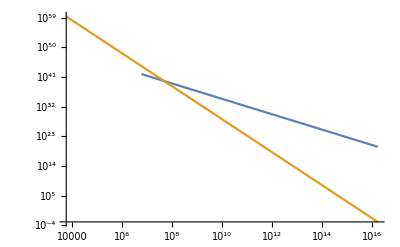

```mathematica
LogLogPlot[{DF[x],GW[x]},{x,rin/1000,rsp}]
```

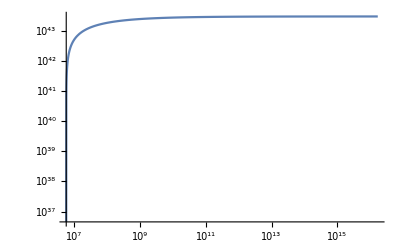

```mathematica
LogLogPlot[{-ΔUdm[r]},{r,rin,rsp},PlotRange->Full]
```

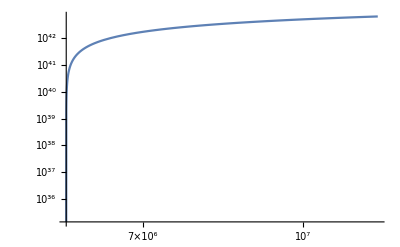

```mathematica
LogLogPlot[{-ΔUdm[r]},{r,rin,2rin},PlotRange->Full]
```

```mathematica
ScientificForm[N[r2,14]]
```

1.4959787070000×10^13

```mathematica
rin
```

5.906×10^6

```mathematica
rsp
```

1.67712×10^16

```mathematica
Ug[b_,a_] = -(G*m1*m2)(1/b-1/a);
Ug[rin*10^5,r2]
```

-4.29×10^41

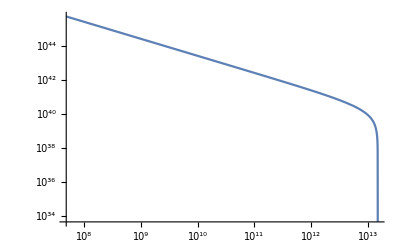

```mathematica
LogLogPlot[{-Ug[r,r2]},{r,Reff,r2},PlotRange->Full]
```

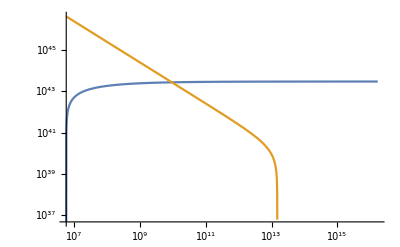

```mathematica
LogLogPlot[{-ΔUdm[r],-Ug[r,r2]},{r,rin,rsp},PlotRange->Full]
```

```mathematica
Rcore= r/. Last[NSolve[{-ΔUdm[r]==-Ug[r,r2]&&r>0&&r<rsp},r]]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

9.46079×10^9

```mathematica
plotStyle={Thick,Blue};
lineStyle={Thick,Orange,Dashed};
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

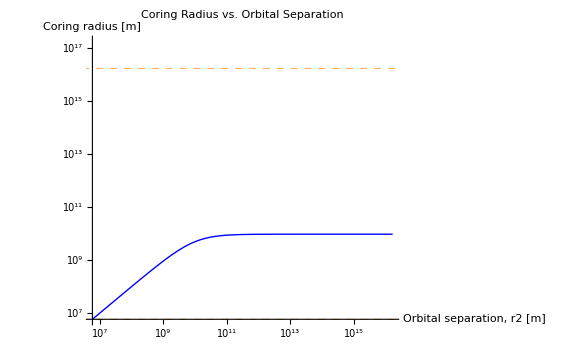

```mathematica
LogLogPlot[{r/.Last[NSolve[{-ΔUdm[r]==-Ug[r,s]&&r>0&&r<rsp},r]]},{s,rin,rsp},AxesLabel->{HoldForm["Orbital separation, r2 [m]"],HoldForm["Coring radius [m]"]},PlotLabel->HoldForm["Coring Radius vs. Orbital Separation"],LabelStyle->{GrayLevel[0],Bold,ImageSize->Large},ImageSize->Large,PlotStyle->Directive[plotStyle],GridLines->{None,{rin,rsp}},GridLinesStyle->Directive[lineStyle],PlotRange->{rin,10rsp}]
```